```mathematica
(* Mathematica*)
```

```mathematica
(*designed 6 hyperbolic group as Orthogonal "zero":
Sum[s[i].Transpose[s[i]],{i,6}]={{0,0},{0,0}};
Casimir invariant matrix :{{2,0},{0,2}}*)
```

```mathematica
s[1]={{I,0},{0,I}}
s[2]={{0,1},{1,0}}
s[3]={{0,-I},{I,0}}
s[4]={{1,0},{0,-1}}
s[5]={{I,I},{-I,I}}/Sqrt[2]
```

{{ⅈ,0},{0,ⅈ}}

{{0,1},{1,0}}

{{0,-ⅈ},{ⅈ,0}}

{{1,0},{0,-1}}

{{ⅈ/(√2),ⅈ/(√2)},{-ⅈ/(√2),ⅈ/(√2)}}

```mathematica
s[6]={{1,1},{-1,1}}/Sqrt[2]
```

{{1/(√2),1/(√2)},{-1/(√2),1/(√2)}}

```mathematica
ka=Table[s[i].{1,1},{i,6}]
```

{{ⅈ,ⅈ},{1,1},{-ⅈ,ⅈ},{1,-1},{ⅈ √2,0},{√2,0}}

```mathematica
Table[Det[s[i]],{i,6}]
```

{-1,-1,-1,-1,-1,1}

```mathematica
Table[Tr[s[i]],{i,6}]
```

{2 ⅈ,0,0,0,ⅈ √2,√2}

```mathematica
(* Casimir Invariant*)
```

```mathematica
Sum[s[i].s[i],{i,6}]
```

{{2,0},{0,2}}

```mathematica
(* orthogonality "zero": singularity/ punctured Polyhedron *)
```

```mathematica
Sum[s[i].Transpose[s[i]],{i,6}]
```

{{0,0},{0,0}}

```mathematica
ka.Transpose[ka]
```

{{-2,2 ⅈ,0,0,-√2,ⅈ √2},{2 ⅈ,2,0,0,ⅈ √2,√2},{0,0,-2,-2 ⅈ,√2,-ⅈ √2},{0,0,-2 ⅈ,2,ⅈ √2,√2},{-√2,ⅈ √2,√2,ⅈ √2,-2,2 ⅈ},{ⅈ √2,√2,-ⅈ √2,√2,2 ⅈ,2}}

```mathematica
Transpose[ka].ka
```

{{0,0},{0,0}}

```mathematica
ca=Table[2*ka[[i]].ka[[j]]/(ka[[i]].ka[[i]]),{i,6},{j,6}]
```

{{2,-2 ⅈ,0,0,√2,-ⅈ √2},{2 ⅈ,2,0,0,ⅈ √2,√2},{0,0,2,2 ⅈ,-√2,ⅈ √2},{0,0,-2 ⅈ,2,ⅈ √2,√2},{√2,-ⅈ √2,-√2,-ⅈ √2,2,-2 ⅈ},{ⅈ √2,√2,-ⅈ √2,√2,2 ⅈ,2}}

```mathematica
Det[ca]
```

0

```mathematica
Tr[ca]
```

12

```mathematica
TableForm[ca]
```

2 | -2 ⅈ | 0 | 0 | √2 | -ⅈ √2
2 ⅈ | 2 | 0 | 0 | ⅈ √2 | √2
0 | 0 | 2 | 2 ⅈ | -√2 | ⅈ √2
0 | 0 | -2 ⅈ | 2 | ⅈ √2 | √2
√2 | -ⅈ √2 | -√2 | -ⅈ √2 | 2 | -2 ⅈ
ⅈ √2 | √2 | -ⅈ √2 | √2 | 2 ⅈ | 2

```mathematica
Eigenvalues[ca]
```

{8,4,0,0,0,0}

```mathematica
p[x_]=ExpandAll[CharacteristicPolynomial[ca,x]/x^4]
```

32-12 x+x^2

```mathematica
Discriminant[p[x],x]
```

16

```mathematica
WeightedAdjacencyGraph[ca]
```

-Graphics-

```mathematica
caj=Floor[Abs[ca]]
```

{{2,2,0,0,1,1},{2,2,0,0,1,1},{0,0,2,2,1,1},{0,0,2,2,1,1},{1,1,1,1,2,2},{1,1,1,1,2,2}}

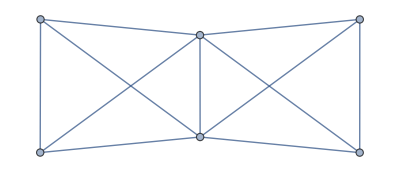

```mathematica
GraphPlot[caj]
```

```mathematica
(* 3d graph:Euler Characteristic {V,F,E}={6,8,11}:V+F-2+2*g=E:6+8-2-n=11:n=1 puncture*)
```

```mathematica
Solve[6+8-2-n==11]
```

{{n→1}}

```mathematica
GraphPlot3D[caj]
```

-Graphics3D-

```mathematica
(*end*)
```

```mathematica
(*Mathematica*)
```

```mathematica
(* 3d BiTetrahedron:Euler Characteristic {V,F,E}={6,8,11}:V+F-2+2*g=E:6+8-2-n=11:n=1 puncture*)
```

```mathematica
{"Tetrahedron",-Graphics3D-,4,4,6,GraphicsComplex[{{0,0,√(2/3)-1/(2 √6)},{-1/(2 √3),-1/2,-1/(2 √6)},{-1/(2 √3),1/2,-1/(2 √6)},{1/(√3),0,-1/(2 √6)}},Polygon[…]]};
```

```mathematica
v=N[{{0,0,√(2/3)-1/(2 √6)},{-1/(2 √3),-1/2,-1/(2 √6)},{-1/(2 √3),1/2,-1/(2 √6)},{1/(√3),0,-1/(2 √6)},{-0.5773502691896258,0.,-0.6123724356957945-0.20412414523193154},{-1.0773502691896258,0.,-0.20412414523193154}}]
```

{{0.,0.,0.612372},{-0.288675,-0.5,-0.204124},{-0.288675,0.5,-0.204124},{0.57735,0.,-0.204124},{-0.57735,0.,-0.816497},{-1.07735,0.,-0.204124}}

```mathematica
g=ListPointPlot3D[v,PlotStyle->Red];
```

```mathematica
e={{2,3,4},{3,2,1},{4,1,2},{1,4,3},{2,3,6},{3,2,5},{6,5,2},{5,6,3}}
```

{{2,3,4},{3,2,1},{4,1,2},{1,4,3},{2,3,6},{3,2,5},{6,5,2},{5,6,3}}

```mathematica
g0=Show[{Graphics3D[GraphicsComplex[v,Polygon[e]]],g},ImageSize->2000,ViewPoint->{2,2,2}];
```

```mathematica
v1=Flatten[Table[Join[Table[(v[[e[[i,j]]]]+v[[e[[i,j+1]]]])/2,{j,Length[e[[i]]]-1}],{(v[[e[[i,1]]]]+v[[e[[i,Length[e[[i]]]]]]])/2}],{i,Length[e]}],1]
```

{{-0.288675,0.,-0.204124},{0.144338,0.25,-0.204124},{0.144338,-0.25,-0.204124},{-0.288675,0.,-0.204124},{-0.144338,-0.25,0.204124},{-0.144338,0.25,0.204124},{0.288675,0.,0.204124},{-0.144338,-0.25,0.204124},{0.144338,-0.25,-0.204124},{0.288675,0.,0.204124},{0.144338,0.25,-0.204124},{-0.144338,0.25,0.204124},{-0.288675,0.,-0.204124},{-0.683013,0.25,-0.204124},{-0.683013,-0.25,-0.204124},{-0.288675,0.,-0.204124},{-0.433013,-0.25,-0.51031},{-0.433013,0.25,-0.51031},{-0.82735,0.,-0.51031},{-0.433013,-0.25,-0.51031},{-0.683013,-0.25,-0.204124},{-0.82735,0.,-0.51031},{-0.683013,0.25,-0.204124},{-0.433013,0.25,-0.51031}}

```mathematica
ListPointPlot3D[{v,v1},PlotStyle->{Red,Green,Blue,Magenta},ImageSize->Medium];
```

```mathematica
Clear[pieces,pieces0]
```

```mathematica
pieces0=Union[N[Join[v,v1]]]
```

{{-1.07735,0.,-0.204124},{-0.82735,0.,-0.51031},{-0.683013,-0.25,-0.204124},{-0.683013,0.25,-0.204124},{-0.57735,0.,-0.816497},{-0.433013,-0.25,-0.51031},{-0.433013,0.25,-0.51031},{-0.288675,-0.5,-0.204124},{-0.288675,0.,-0.204124},{-0.288675,0.5,-0.204124},{-0.144338,-0.25,0.204124},{-0.144338,0.25,0.204124},{0.,0.,0.612372},{0.144338,-0.25,-0.204124},{0.144338,0.25,-0.204124},{0.288675,0.,0.204124},{0.57735,0.,-0.204124}}

```mathematica
Length[pieces0]
```

17

```mathematica
wa=Table[N[Max[Table[pieces0[[i,j]],{i,Length[pieces0]}]]],{j,3}]
```

{0.57735,0.5,0.612372}

```mathematica
pieces=Union[Table[{pieces0[[i,1]]/wa[[1]],pieces0[[i,2]]/wa[[2]],pieces0[[i,3]]/wa[[3]]},{i,Length[pieces0]}]]
```

{{-1.86603,0.,-0.333333},{-1.43301,0.,-0.833333},{-1.18301,-0.5,-0.333333},{-1.18301,0.5,-0.333333},{-1.,0.,-1.33333},{-0.75,-0.5,-0.833333},{-0.75,0.5,-0.833333},{-0.5,-1.,-0.333333},{-0.5,0.,-0.333333},{-0.5,1.,-0.333333},{-0.25,-0.5,0.333333},{-0.25,0.5,0.333333},{0.,0.,1.},{0.25,-0.5,-0.333333},{0.25,0.5,-0.333333},{0.5,0.,0.333333},{1.,0.,-0.333333}}

```mathematica
Length[pieces]
```

17

```mathematica
Table[N[Max[Table[pieces[[i,j]],{i,Length[pieces]}]]],{j,3}]
```

{1.,1.,1.}

```mathematica
ListPointPlot3D[pieces,ColorFunction->"Rainbow",ImageSize->Medium];
```

```mathematica
Length[pieces]
```

17

```mathematica
N[Log[Length[pieces]]/Log[3]]
```

2.5789

```mathematica
Clear[menger1]
```

```mathematica
menger1[cornerPt_, sideLen_, n_] :=
  menger1[cornerPt + #1*(sideLen/3.), sideLen/3.,n - 1] & /@pieces;
 menger1[cornerPt_, sideLen_, 0] :=
  {Opacity[0.95],ColorData["Rainbow"][N[2*Apply[Plus,cornerPt]]],EdgeForm[],Cuboid[cornerPt, cornerPt + sideLen*{1, 1, 1}]};
```

```mathematica
(*Show[Graphics3D[Flatten[menger1[{0, 0, 0}, 1,2]]],Boxed->False,ImageSize->Full,AspectRatio->1,ViewPoint->{2,2,2},Background->Black]*)
```

```mathematica
g1=Show[Graphics3D[Flatten[menger1[{0, 0, 0}, 1,4]]],Boxed->False,ImageSize->2000,AspectRatio->1,ViewPoint->{2,2,2},Background->Black];
```

```mathematica
g2=Show[g1,ViewPoint->Above];
```

```mathematica
g3=Show[g1,ViewPoint->{1.3, -2.4, 2.}];
```

```mathematica
g4=Show[g1,ViewPoint->Right];
g5=Show[g1,ViewPoint->Front];
```

```mathematica
Export["Menger_BiTetrahedron_ratio3_level4_Rainbow_grid.jpg",GraphicsGrid[{{g0,g1,g2}, 
 {g3,g4,g5}},ImageSize->4000]]
```

```mathematica
Export["Menger_BiTetrahedron_ratio3_level4_Rainbow_g1.ply" ,g1]
```

$Aborted

```mathematica
Export["Menger_BiTetrahedron_ratio3_level4_Rainbow_g1.stl" ,g1]
```

```mathematica
(*end*)
```